```mathematica
m = 1000
```

1000

```mathematica
a = 2
```

2

```mathematica
p0 = 1
```

1

```mathematica
G[q1_,q_] = Sqrt[m/(2*Pi*t*I)]*Exp[(I*m(q1 - q)^2)/(2*t)]
```

10 ⅇ^((500 ⅈ (-q+q1)^2)/t) √(5/π) √(-ⅈ/t)

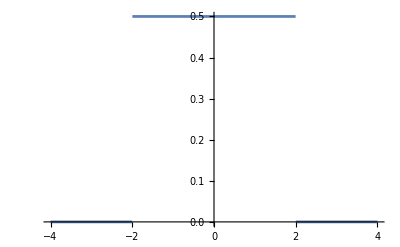

```mathematica
Plot[(1/2)*(HeavisideTheta[q+a]-HeavisideTheta[q-a]),{q,-2*a,2*a}]
```

```mathematica
psiFreeP[q_] = Exp[I*p0*q ]*((Exp[-q^2/a^2] - Exp[-1])^4)*((1/2)*(HeavisideTheta[q+a]-HeavisideTheta[q-a]))
```

1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])

```mathematica
rhoPsiFreeP[q_]=(Re[psiFreeP[q]]^2)+(Im[psiFreeP[q]]^2)
```

1/4 Im[ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])]^2+1/4 Re[ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])]^2

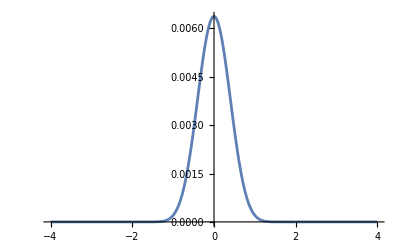

```mathematica
Plot[rhoPsiFreeP[q],{q,-2*a,2*a},PlotRange->All]
```

```mathematica
rhoDpsiFreeP[q_] = (Re[D[psiFreeP[q],q]]^2)+(Im[D[psiFreeP[q],q]]^2)
```

(Im[1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-DiracDelta[-2+q]+DiracDelta[2+q])-ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 q (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])]+1/2 Re[ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])])^2+(-1/2 Im[ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])]+Re[1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-DiracDelta[-2+q]+DiracDelta[2+q])-ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 q (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])])^2

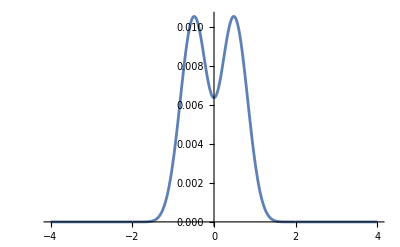

```mathematica
Plot[rhoDpsiFreeP[q],{q,-2*a,2*a},PlotRange->All]
```

```mathematica
rhoDDpsiFreeP[q_] = (Re[D[psiFreeP[q],q,q]]^2)+(Im[D[psiFreeP[q],q,q]]^2)
```

(Im[-2 ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 q (-DiracDelta[-2+q]+DiracDelta[2+q])-ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])-1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])-ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 (ⅈ-q/2) q (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])+3/2 ⅇ^(ⅈ q-q^2/2) (-1/ⅇ+ⅇ^(-q^2/4))^2 q^2 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])+1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-DiracDelta'[-2+q]+DiracDelta'[2+q])]+Re[ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-DiracDelta[-2+q]+DiracDelta[2+q])]-Re[ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 q (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])])^2+(-Im[ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-DiracDelta[-2+q]+DiracDelta[2+q])]+Im[ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 q (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])]+Re[-2 ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 q (-DiracDelta[-2+q]+DiracDelta[2+q])-ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])-1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])-ⅇ^(ⅈ q-q^2/4) (-1/ⅇ+ⅇ^(-q^2/4))^3 (ⅈ-q/2) q (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])+3/2 ⅇ^(ⅈ q-q^2/2) (-1/ⅇ+ⅇ^(-q^2/4))^2 q^2 (-HeavisideTheta[-2+q]+HeavisideTheta[2+q])+1/2 ⅇ^(ⅈ q) (-1/ⅇ+ⅇ^(-q^2/4))^4 (-DiracDelta'[-2+q]+DiracDelta'[2+q])])^2

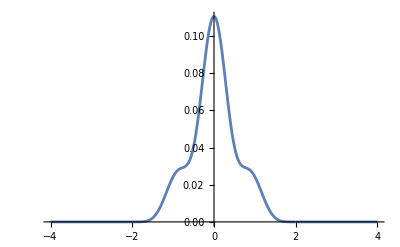

```mathematica
Plot[rhoDDpsiFreeP[q],{q,-2*a,2*a},PlotRange->All]
```

```mathematica
Integrate[psiFreeP[q]*G[q1,q],{q,-a,+a},Assumptions->t>=0]
```

1/(√(ⅈ t))5 √(5/π) (ⅇ^((500 ⅈ q1^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q1-(500 ⅈ q1^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-2000-1000 q1+t) Erf[(√(-ⅈ (-2000-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (-2000-1000 q1+t)^2))+((1/2-ⅈ/2) √(π/2) (-1000 q1+t) Erf[(√(-ⅈ (-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q1+t)^2)))+ⅇ^(-(-ⅈ+(1000 ⅈ q1)/t)^2/(4 (-1+(500 ⅈ)/t))) ((ⅈ √π √t √(-(2000+1000 q1-(1-4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000+1000 q1-(1-4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000+2000 q1-(2-8 ⅈ) t)+(ⅈ √π √t √(-(-1000 q1+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q1+t)))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q1^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q1)/((-1/2+(500 ⅈ)/t) t)) (-(((2/5-ⅈ/5) √(π/2) √t √(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q1-t)^2)/(-1000 ⅈ+t)) Erf[(√(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q1-t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400+800 ⅈ)+(200+400 ⅈ) q1-t))+(ⅈ √(π/2) √t √(-(-1000 q1+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q1+t))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q1^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q1)/((-1/4+(500 ⅈ)/t) t)) (-(((1-ⅈ) √(π/2) √t √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q1-t)^2)/(-2000 ⅈ+t)) Erf[(√2 √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q1-t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000+1000 ⅈ)+(500+500 ⅈ) q1-t))+(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q1+t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q1^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q1)/((-3/4+(500 ⅈ)/t) t)) (-(((3/5-ⅈ/5) √(π/2) √t √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q1-t)^2)/(-2000 ⅈ+3 t)) Erf[(√2 √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q1-t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200+600 ⅈ)+(100+300 ⅈ) q1-t))+(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q1+t)))+ⅇ^((500 ⅈ q1^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q1-(500 ⅈ q1^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-1000 q1+t) Erf[(√(-ⅈ (-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q1+t)^2))+((1/2-ⅈ/2) √(π/2) (2000-1000 q1+t) Erf[(√(-ⅈ (2000-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (2000-1000 q1+t)^2)))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q1^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q1)/((-1/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q1+t)+((1+ⅈ) √(π/2) √t √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q1+t)^2)/(-2000 ⅈ+t)) Erf[(√2 √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q1+t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000-1000 ⅈ)-(500-500 ⅈ) q1+t))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q1^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q1)/((-1/2+(500 ⅈ)/t) t)) (-(ⅈ √(π/2) √t √(-(-1000 q1+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q1+t)+((2/5+ⅈ/5) √(π/2) √t √(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q1+t)^2)/(-1000 ⅈ+t)) Erf[(√(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q1+t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400-800 ⅈ)-(200-400 ⅈ) q1+t))+ⅇ^(-(ⅈ-(1000 ⅈ q1)/t)^2/(4 (-1+(500 ⅈ)/t))) (-(ⅈ √π √t √(-(-1000 q1+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q1+t))+(ⅈ √π √t √(-(2000-1000 q1+(1+4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000-1000 q1+(1+4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000-2000 q1+(2+8 ⅈ) t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q1^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q1)/((-3/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q1+t)+((3/5+ⅈ/5) √π √t √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q1+t)^2)/(-4000 ⅈ+6 t)) Erf[(√2 √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q1+t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200-600 ⅈ)-(100-300 ⅈ) q1+t))))

```mathematica
psiFreePT[q1_,t_] = %
```

1/(√(ⅈ t))5 √(5/π) (ⅇ^((500 ⅈ q1^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q1-(500 ⅈ q1^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-2000-1000 q1+t) Erf[(√(-ⅈ (-2000-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (-2000-1000 q1+t)^2))+((1/2-ⅈ/2) √(π/2) (-1000 q1+t) Erf[(√(-ⅈ (-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q1+t)^2)))+ⅇ^(-(-ⅈ+(1000 ⅈ q1)/t)^2/(4 (-1+(500 ⅈ)/t))) ((ⅈ √π √t √(-(2000+1000 q1-(1-4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000+1000 q1-(1-4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000+2000 q1-(2-8 ⅈ) t)+(ⅈ √π √t √(-(-1000 q1+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q1+t)))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q1^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q1)/((-1/2+(500 ⅈ)/t) t)) (-(((2/5-ⅈ/5) √(π/2) √t √(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q1-t)^2)/(-1000 ⅈ+t)) Erf[(√(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q1-t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400+800 ⅈ)+(200+400 ⅈ) q1-t))+(ⅈ √(π/2) √t √(-(-1000 q1+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q1+t))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q1^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q1)/((-1/4+(500 ⅈ)/t) t)) (-(((1-ⅈ) √(π/2) √t √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q1-t)^2)/(-2000 ⅈ+t)) Erf[(√2 √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q1-t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000+1000 ⅈ)+(500+500 ⅈ) q1-t))+(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q1+t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q1^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q1)/((-3/4+(500 ⅈ)/t) t)) (-(((3/5-ⅈ/5) √(π/2) √t √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q1-t)^2)/(-2000 ⅈ+3 t)) Erf[(√2 √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q1-t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200+600 ⅈ)+(100+300 ⅈ) q1-t))+(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q1+t)))+ⅇ^((500 ⅈ q1^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q1-(500 ⅈ q1^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-1000 q1+t) Erf[(√(-ⅈ (-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q1+t)^2))+((1/2-ⅈ/2) √(π/2) (2000-1000 q1+t) Erf[(√(-ⅈ (2000-1000 q1+t)^2))/(20 √5 √t)])/(√(-ⅈ (2000-1000 q1+t)^2)))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q1^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q1)/((-1/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q1+t)+((1+ⅈ) √(π/2) √t √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q1+t)^2)/(-2000 ⅈ+t)) Erf[(√2 √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q1+t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000-1000 ⅈ)-(500-500 ⅈ) q1+t))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q1^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q1)/((-1/2+(500 ⅈ)/t) t)) (-(ⅈ √(π/2) √t √(-(-1000 q1+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q1+t)+((2/5+ⅈ/5) √(π/2) √t √(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q1+t)^2)/(-1000 ⅈ+t)) Erf[(√(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q1+t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400-800 ⅈ)-(200-400 ⅈ) q1+t))+ⅇ^(-(ⅈ-(1000 ⅈ q1)/t)^2/(4 (-1+(500 ⅈ)/t))) (-(ⅈ √π √t √(-(-1000 q1+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q1+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q1+t))+(ⅈ √π √t √(-(2000-1000 q1+(1+4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000-1000 q1+(1+4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000-2000 q1+(2+8 ⅈ) t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q1^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q1)/((-3/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q1+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q1+t)+((3/5+ⅈ/5) √π √t √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q1+t)^2)/(-4000 ⅈ+6 t)) Erf[(√2 √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q1+t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200-600 ⅈ)-(100-300 ⅈ) q1+t))))

```mathematica
rhoPsiFreePT[q_,t_]=(Re[psiFreePT[q,t]]^2)+(Im[psiFreePT[q,t]]^2)
```

1/π 125 (Im[1/(√(ⅈ t))(ⅇ^((500 ⅈ q^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q-(500 ⅈ q^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-2000-1000 q+t) Erf[(√(-ⅈ (-2000-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (-2000-1000 q+t)^2))+((1/2-ⅈ/2) √(π/2) (-1000 q+t) Erf[(√(-ⅈ (-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q+t)^2)))+ⅇ^(-(-ⅈ+(1000 ⅈ q)/t)^2/(4 (-1+(500 ⅈ)/t))) ((ⅈ √π √t √(-(2000+1000 q-(1-4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000+1000 q-(1-4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000+2000 q-(2-8 ⅈ) t)+(ⅈ √π √t √(-(-1000 q+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q+t)))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q)/((-1/2+(500 ⅈ)/t) t)) (-(((2/5-ⅈ/5) √(π/2) √t √(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q-t)^2)/(-1000 ⅈ+t)) Erf[(√(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q-t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400+800 ⅈ)+(200+400 ⅈ) q-t))+(ⅈ √(π/2) √t √(-(-1000 q+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q+t))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q)/((-1/4+(500 ⅈ)/t) t)) (-(((1-ⅈ) √(π/2) √t √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q-t)^2)/(-2000 ⅈ+t)) Erf[(√2 √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q-t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000+1000 ⅈ)+(500+500 ⅈ) q-t))+(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q+t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q)/((-3/4+(500 ⅈ)/t) t)) (-(((3/5-ⅈ/5) √(π/2) √t √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q-t)^2)/(-2000 ⅈ+3 t)) Erf[(√2 √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q-t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200+600 ⅈ)+(100+300 ⅈ) q-t))+(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q+t)))+ⅇ^((500 ⅈ q^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q-(500 ⅈ q^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-1000 q+t) Erf[(√(-ⅈ (-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q+t)^2))+((1/2-ⅈ/2) √(π/2) (2000-1000 q+t) Erf[(√(-ⅈ (2000-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (2000-1000 q+t)^2)))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q)/((-1/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q+t)+((1+ⅈ) √(π/2) √t √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q+t)^2)/(-2000 ⅈ+t)) Erf[(√2 √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q+t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000-1000 ⅈ)-(500-500 ⅈ) q+t))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q)/((-1/2+(500 ⅈ)/t) t)) (-(ⅈ √(π/2) √t √(-(-1000 q+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q+t)+((2/5+ⅈ/5) √(π/2) √t √(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q+t)^2)/(-1000 ⅈ+t)) Erf[(√(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q+t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400-800 ⅈ)-(200-400 ⅈ) q+t))+ⅇ^(-(ⅈ-(1000 ⅈ q)/t)^2/(4 (-1+(500 ⅈ)/t))) (-(ⅈ √π √t √(-(-1000 q+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q+t))+(ⅈ √π √t √(-(2000-1000 q+(1+4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000-1000 q+(1+4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000-2000 q+(2+8 ⅈ) t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q)/((-3/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q+t)+((3/5+ⅈ/5) √π √t √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q+t)^2)/(-4000 ⅈ+6 t)) Erf[(√2 √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q+t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200-600 ⅈ)-(100-300 ⅈ) q+t))))])^2+1/π 125 (Re[1/(√(ⅈ t))(ⅇ^((500 ⅈ q^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q-(500 ⅈ q^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-2000-1000 q+t) Erf[(√(-ⅈ (-2000-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (-2000-1000 q+t)^2))+((1/2-ⅈ/2) √(π/2) (-1000 q+t) Erf[(√(-ⅈ (-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q+t)^2)))+ⅇ^(-(-ⅈ+(1000 ⅈ q)/t)^2/(4 (-1+(500 ⅈ)/t))) ((ⅈ √π √t √(-(2000+1000 q-(1-4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000+1000 q-(1-4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000+2000 q-(2-8 ⅈ) t)+(ⅈ √π √t √(-(-1000 q+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q+t)))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q)/((-1/2+(500 ⅈ)/t) t)) (-(((2/5-ⅈ/5) √(π/2) √t √(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q-t)^2)/(-1000 ⅈ+t)) Erf[(√(((3+4 ⅈ) ((400+800 ⅈ)+(200+400 ⅈ) q-t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400+800 ⅈ)+(200+400 ⅈ) q-t))+(ⅈ √(π/2) √t √(-(-1000 q+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q+t))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q)/((-1/4+(500 ⅈ)/t) t)) (-(((1-ⅈ) √(π/2) √t √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q-t)^2)/(-2000 ⅈ+t)) Erf[(√2 √((ⅈ ((1000+1000 ⅈ)+(500+500 ⅈ) q-t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000+1000 ⅈ)+(500+500 ⅈ) q-t))+(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q+t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q)/((-3/4+(500 ⅈ)/t) t)) (-(((3/5-ⅈ/5) √(π/2) √t √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q-t)^2)/(-2000 ⅈ+3 t)) Erf[(√2 √(((4+3 ⅈ) ((200+600 ⅈ)+(100+300 ⅈ) q-t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200+600 ⅈ)+(100+300 ⅈ) q-t))+(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q+t)))+ⅇ^((500 ⅈ q^2)/t) (1/(10 √5)ⅇ^(-4+ⅈ q-(500 ⅈ q^2)/t-(ⅈ t)/2000) √(ⅈ t) (-((1/2-ⅈ/2) √(π/2) (-1000 q+t) Erf[(√(-ⅈ (-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (-1000 q+t)^2))+((1/2-ⅈ/2) √(π/2) (2000-1000 q+t) Erf[(√(-ⅈ (2000-1000 q+t)^2))/(20 √5 √t)])/(√(-ⅈ (2000-1000 q+t)^2)))-4 ⅇ^(-3+1/(4 (-1/4+(500 ⅈ)/t))+(250000 q^2)/((-1/4+(500 ⅈ)/t) t^2)-(500 q)/((-1/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+t)))/(√t)])/(-1000 q+t)+((1+ⅈ) √(π/2) √t √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q+t)^2)/(-2000 ⅈ+t)) Erf[(√2 √(-(ⅈ ((1000-1000 ⅈ)-(500-500 ⅈ) q+t)^2)/(-2000 ⅈ+t)))/(√t)])/((1000-1000 ⅈ)-(500-500 ⅈ) q+t))+6 ⅇ^(-2+1/(4 (-1/2+(500 ⅈ)/t))+(250000 q^2)/((-1/2+(500 ⅈ)/t) t^2)-(500 q)/((-1/2+(500 ⅈ)/t) t)) (-(ⅈ √(π/2) √t √(-(-1000 q+t)^2/(-1000 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-1000 ⅈ+t)))/(√2 √t)])/(-1000 q+t)+((2/5+ⅈ/5) √(π/2) √t √(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q+t)^2)/(-1000 ⅈ+t)) Erf[(√(((3-4 ⅈ) ((400-800 ⅈ)-(200-400 ⅈ) q+t)^2)/(-1000 ⅈ+t)))/(√2 √t)])/((400-800 ⅈ)-(200-400 ⅈ) q+t))+ⅇ^(-(ⅈ-(1000 ⅈ q)/t)^2/(4 (-1+(500 ⅈ)/t))) (-(ⅈ √π √t √(-(-1000 q+t)^2/(-500 ⅈ+t)) Erf[(√(-(-1000 q+t)^2/(-500 ⅈ+t)))/(2 √t)])/(2 (-1000 q+t))+(ⅈ √π √t √(-(2000-1000 q+(1+4 ⅈ) t)^2/(-500 ⅈ+t)) Erf[(√(-(2000-1000 q+(1+4 ⅈ) t)^2/(-500 ⅈ+t)))/(2 √t)])/(4000-2000 q+(2+8 ⅈ) t))-4 ⅇ^(-1+1/(4 (-3/4+(500 ⅈ)/t))+(250000 q^2)/((-3/4+(500 ⅈ)/t) t^2)-(500 q)/((-3/4+(500 ⅈ)/t) t)) (-(ⅈ √π √t √(-(-1000 q+t)^2/(-2000 ⅈ+3 t)) Erf[(√(-(-1000 q+t)^2/(-2000 ⅈ+3 t)))/(√t)])/(-1000 q+t)+((3/5+ⅈ/5) √π √t √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q+t)^2)/(-4000 ⅈ+6 t)) Erf[(√2 √(((4-3 ⅈ) ((200-600 ⅈ)-(100-300 ⅈ) q+t)^2)/(-2000 ⅈ+3 t)))/(√t)])/((200-600 ⅈ)-(100-300 ⅈ) q+t))))])^2

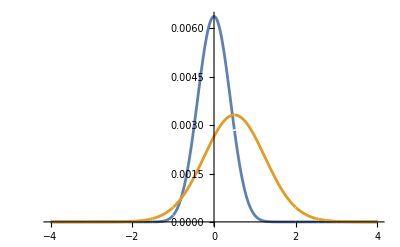

```mathematica
Plot[{rhoPsiFreeP[q1],rhoPsiFreePT[q1,500]},{q1,-2*a,2*a},PlotRange->All]
```

```mathematica
N[rhoPsiFreePT[2,500]]
```

0.000451869

```mathematica
N[rhoPsiFreeP[3]]
```

0.

```mathematica
N[rhoPsiFreeP[1]]
```

0.00020324

```mathematica
N[rhoPsiFreePT[10,500]]
```

2.38117×10^-14

```mathematica
500*(p0/m)
```

1/2

```mathematica
FindMaximum[rhoPsiFreePT[q,500],{q,1}]
```

{0.00331843,{q→0.5}}

```mathematica
FindMaximum[rhoPsiFreeP[q],{q,1}]
```

{0.00637293,{q→-7.97578×10^-9}}

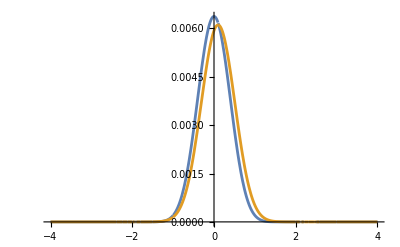

```mathematica
Plot[{rhoPsiFreeP[q1],rhoPsiFreePT[q1,100]},{q1,-2*a,2*a},PlotRange->All]
```

```mathematica
FindMaximum[rhoPsiFreePT[q,100],{q,0.5}]
```

{0.00611018,{q→0.1}}